This function takes a value of gτ and outputs a plot in m_W' vs g_q showing :
- RD/RD^* fits 
- Exclusive limits on σ(p p→ W'+X) x BR(W’ τ ν) where X is a 1 or 2 b-jets
	Calculation done in MG+Pythia using the WZPrime UFO
- If you end up using this notebook for some reason, you may cite Abdullah et al 1804.xxxx

```mathematica
wpplots[gτ_]:=Block[{},

(*Calculation of RD and RD* Regions*)
subs = {Gf ->  1.16 10^-5,Vcb-> 0.04};
Cbcl = {(4 Gf)/(√2)Vcb ,(4 Gf)/(√2)Vcb ,(4 Gf)/(√2)Vcb +gτ gp/MWp^2};
(*Equation (74) in Boucenna 1608.01349*)
RDFactor = (2 Cbcl[[3]]^2)/(Cbcl[[1]]^2+ Cbcl[[2]]^2);

gpsolv = gp/.(Solve[Evaluate[RDFactor] th == exp,gp]/.subs)[[1]]//Quiet;
gpfit[MWp_,th_,exp_]:= Evaluate[gpsolv];
(*Values below taken from Kamali 1801.08259*)
RDSM = 0.298;
RDSMerror = 0.003;
RDExp = 0.407;
RDExperror = √(0.039^2+0.024^2);
RDSSM = 0.255;
RDSSMerror = 0.004;
RDSExp = 0.304;
RDSExperror = √(0.013^2+0.007^2);
RDplot = LogPlot[{gpfit[mwp,RDSM-RDSMerror,RDExp+RDExperror],gpfit[mwp,RDSM+RDSMerror,RDExp-RDExperror]},{mwp,200,1000},PlotStyle->None,Filling->{1->{2}},FillingStyle->Directive[Opacity[0.5],Blue],
PlotLegends->Automatic];
RDSplot = LogPlot[{gpfit[mwp,RDSSM-RDSSMerror,RDSExp+RDSExperror],gpfit[mwp,RDSSM+RDSSMerror,RDSExp-RDSExperror]},{mwp,200,1000},PlotStyle->None,Filling->{1->{2}},FillingStyle->Directive[Opacity[0.5],Green]];


(*Exclusice Limits*)
 (*W' Masses*)
Mwp = {200,250,300,350,500,750,1000};
(*Signal selection efficiency*)
eff = {2.31 10^-2,0.176,0.626,0.965,2.56,4.44,5.15} /100; 
(*σ(p p -> W' (+1b, +2b))x BR(W'-> τ ν) (pb)*)
(*Assumes 0.1 couplings -> BR(W'-> τ ν) = 0.25*)
σ = {7.8,3.4,1.7,0.92,0.22,0.035,0.0084} ;  
(*{Background, σ (pb), efficiency}*)
Bkgrnd = {
{"tt",205,3.62 10^-4},
{"t",179.9,3.31 10^-5},
{"W+j",501,5.21 10^-5},
{"DY+j",167.2,8.22 10^-5},
{"WW",65.23,5.83 10^-6},
{"ZZ",24.77,4.37 10^-5},
{"WZ",9.558, 1.85 10^-5}};
(*Total background for 1 fb^-1*)
B = Sum[Bkgrnd[[i,2]] Bkgrnd[[i,3]],{i,1,7}]  10^3;

(*Setting up the coupling dependence*)
σg = Table[(g/0.1)^2 σ[[i]] gτ^2/(gτ^2+3 g^2)/0.25,{i,1,7}];
(*The signal for 1 fb^-1*)
S = Table[σg[[i]] 10^3  eff[[i]],{i,1,7}];

(*Now we calculate the limit by setting S/(√(S+B)) = 3 for L = 30, 300, 3000 fb^-1*)
glim = Table[Abs[Re[g]]/.NSolve[{S[[i]]/(√(S[[i]]+B)) √L==3},g][[1]],{i,1,7},{L,{30,300,3000}}]//Quiet;

(*plot, plot plot*)
Lim30 = Table[{Mwp[[i]],Transpose[glim][[1]][[i]]},{i,1,7}];
plot30 = ListLogPlot[Lim30,Joined-> True,PlotStyle->{Black,Thick}];
Lim300 = Table[{Mwp[[i]],Transpose[glim][[2]][[i]]},{i,1,7}];
plot300=ListLogPlot[Lim300,Joined-> True,PlotStyle->{Black,Thick}];
Lim3000 = Table[{Mwp[[i]],Transpose[glim][[3]][[i]]},{i,1,7}];
plot3000 = ListLogPlot[Lim3000,Joined-> True,PlotStyle-> {Black,Thick}];

(*Next we recast inclusive limits from ATLAS and CMS*)

(*ATLAS Limits 13 TeV, L = 36.1 fb^-1 1801.06992*)
MwpAT = {500,600,800,1000};
LimitsAT = {0.6,0.3,0.1,0.05}; (*Limits from paper*)
σAT = {0.22,0.096,0.025,0.0084}; (*Our MG+Pythia calculation*)
σgIncAT = Table[(g/0.1)^2 σAT[[i]] gτ^2/(gτ^2+3 g^2)/0.25,{i,1,4}];
glimIncAT = Table[Abs[Re[g]]/.NSolve[σgIncAT[[i]]==LimitsAT[[i]],g][[1]],{i,1,4}]//Quiet;
LimIncAT = Table[{MwpAT[[i]],glimIncAT[[i]]},{i,1,4}];
plotIncAT = ListLogPlot[LimIncAT,Joined-> True,PlotStyle->{Red,Thick,Dotted}];


(*CMS Limits 8 TeV, L = 19.7 fb^-1 1508.04308*)
MwpInc8 = {300,500,800,900,1100};
LimitsInc8 = {5,0.15, 0.02, 0.013,0.008};
σInc8 = {0.59,0.059,0.0055,0.0029,0.00089} ;
(*σ(p p -> W' (+1b, +2b))x BR(W'-> τ ν) (pb)*)
(*Assumes 0.1 couplings -> BR(W'-> τ ν) = 0.25*)
σgInc8 = Table[(g/0.1)^2 σInc8[[i]] gτ^2/(gτ^2+3 g^2)/0.25,{i,1,5}];
glimInc8 = Table[Abs[Re[g]]/.NSolve[σgInc8[[i]]==LimitsInc8[[i]],g][[1]],{i,1,5}]//Quiet;
LimInc8 = Table[{MwpInc8[[i]],glimInc8[[i]]},{i,1,5}];
plotInc8 = ListLogPlot[LimInc8,Joined-> True,PlotStyle->{Magenta,Thick,Dashed}];


Graphics[Show[RDplot,RDSplot,plot30,plot300,plot3000,plotInc8,plotIncAT,
PlotRange->{{200,1000},{Log[0.005],Log[0.8]}},
Frame->{{True,True},{True,True}},
AxesOrigin-> {200,Log[0.005]},ImageSize-> 600,
FrameTicksStyle->{Directive[Black,FontSize->15,FontFamily-> "Times"],
Directive[Black,FontSize->15,FontFamily-> "Times"]},
FrameLabel->{Style["m_W'",20,FontFamily->"Times",Black],
Style["g_q",20,FontFamily->"Times",Black]}]]];
```

```mathematica
Manipulate[wpplots[gτ],{gτ,0.01,1}]
```

```mathematica
wpplots[0.35]
```

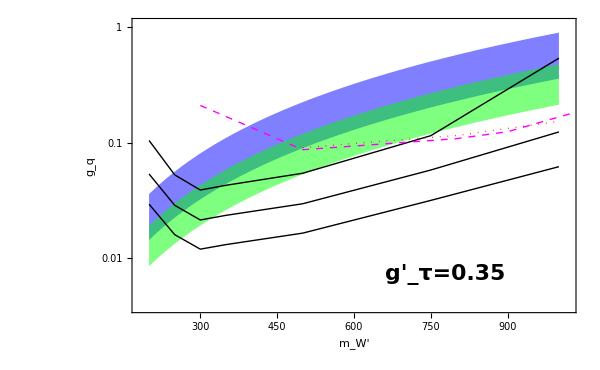

```mathematica
wpplots[0.65]
```

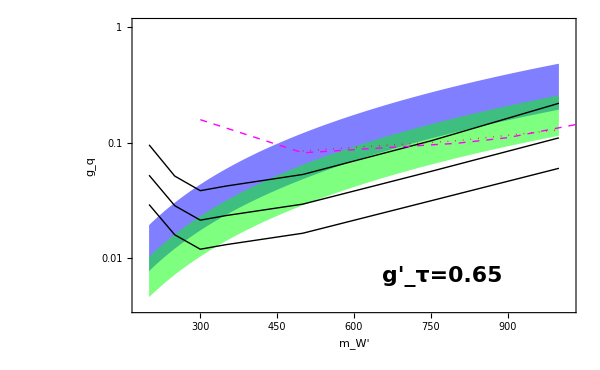

```mathematica
wpplots[1]
```

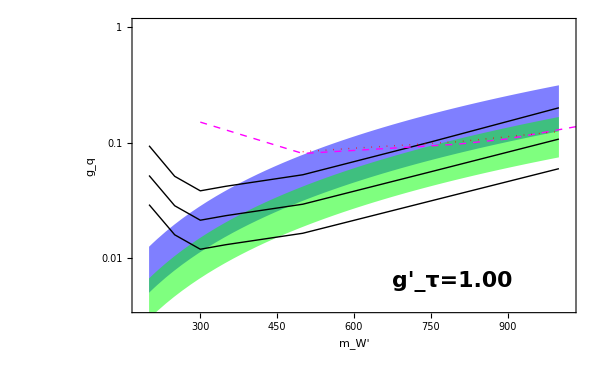

```mathematica
(*You can generate a GIF for various values of gτ using the command below*)
blah =Table[Show[wpplots[gτ],Graphics[Text[Style["gτ="Text[gτ],FontSize->20],{900,Log[0.01]}]]],{gτ,{0.01,0.05,0.075,0.1,0.15,0.2,0.5,0.8,1}}];
Export["WpLimits.gif",blah,"DisplayDurations"->1,"AnimationRepetitions"->Infinity,ImageSize->700]
```

```mathematica
(*Fitting the production cross section*)
```

InterpolatingFunction[…]

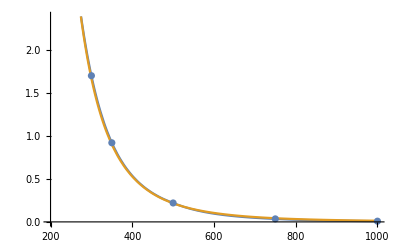

```mathematica
mσ = Table[{Mwp[[i]],σ[[i]]},{i,1,7}];
mσinv = Table[{Mwp[[i]],1/σ[[i]]},{i,1,7}];
blah=Interpolation[mσinv,InterpolationOrder->3]
Show[Plot[{1/blah[x],135 (10^2)^4/x^4},{x,200,1000}],ListPlot[mσ]]
(*i.e. σ(pp->W'+(0,1,2)b)xBR(W'->τν) = 135 (gq/0.1)^2 (gτ/0.1)^2 (gτ^2/(gτ^2+3 gq^2))/0.25 (100/MWp)^4 pb*)
```